```mathematica
ClearAll["Global`*"];
ClearAll[m];
```

```mathematica
data=Association[];
data[{a->0.3,μ->3000}]={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
data[{Qm->0.6,μ->3000}]={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
data[{a->0.3,μ->0}]={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
data[{Qm->0.6,μ->0}]={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
ExtractData[data_]:=Module[{shadow,measure,lines,line,xmin,xmax,ymin,ymax,xc,yc,Dc,Dx,Dy,newLine,polarLine,r,rbar,σr,LHratio,area},
shadow=EdgeDetect[data,30];(*should test carefully before changing it*)
line=PixelValuePositions[shadow,1]-512;
{xmin,xmax}=MinMax[line⟦All,1⟧];
{ymin,ymax}=MinMax[line⟦All,2⟧];
{xc,yc}={(xmin+xmax)/2,(ymin+ymax)/2};
line=#-{xc,yc}&/@line;
Dc=Abs@xc;
{Dx,Dy}={xmax-xmin,ymax-ymin};
LHratio=Dx/Dy;
newLine=Union[line,SameTest->(Norm[#1-#2]<5&)];(*remove very close points*)
polarLine=DeleteDuplicates[{ArcTan[#⟦1⟧,#⟦2⟧],√((#⟦1⟧)^2+(#⟦2⟧)^2)}&/@newLine,#1⟦1⟧==#2⟦1⟧&];
polarLine=Join[Select[SortBy[polarLine,First],#⟦1⟧>0&],{#⟦1⟧+2π,#⟦2⟧}&/@Select[SortBy[polarLine,First],#⟦1⟧<0&]];
r02pi=polarLine[[1,2]];
AppendTo[polarLine,{0,r02pi}];
AppendTo[polarLine,{2π,r02pi}];
r=Interpolation[polarLine,InterpolationOrder->0];
rbar=NIntegrate[r[α]/(2π),{α,0,2π}];
σr=√NIntegrate[(r[α]-rbar)^2/(2π),{α,0,2π}];
area=NIntegrate[1/2 r[α]^2,{α,0,2π}];
{xmin,xmax,ymin,ymax,xc,yc,newLine,r,Dc,Dx,Dy,LHratio,rbar,σr,area}];
```

```mathematica
shapedata=Map[ExtractData,data,{2}]
```

```mathematica
shrink=Association[];
shrink[{a->0.3,μ->3000}]=Table[(shapedata[{a->0.3,μ->3000}][[m,-1]])/(shapedata[{a->0.3,μ->0}][[m,-1]]),{m,1,16}];
shrink[{Qm->0.6,μ->3000}]=Table[(shapedata[{Qm->0.6,μ->3000}][[m,-1]])/(shapedata[{Qm->0.6,μ->0}][[m,-1]]),{m,1,14}];
shrink
```

<|{a→0.3,μ→3000}→{1.06427,1.24171,1.48465,1.75572,2.04102,2.33387,2.64112,2.97579,3.30507,3.66351,4.03768,4.4384,4.88585,5.36461,5.90865,6.56192},{Qm→0.6,μ→3000}→{4.41239,4.42468,4.4216,4.42866,4.43253,4.4384,4.44985,4.4694,4.51024,4.53754,4.55252,4.57274,4.62949,4.6814}|>

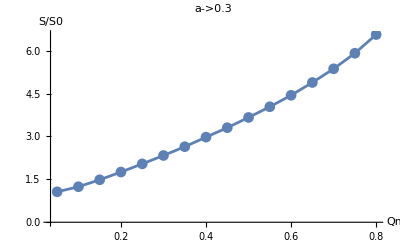

```mathematica
ListLinePlot[Table[{0.05m,shrink[{a->0.3,μ->3000}][[m]]},{m,1,16}],AxesLabel->{"Qm","S/S0"},PlotRange->All,PlotMarkers->Automatic,PlotLabel->"a->0.3"]
```

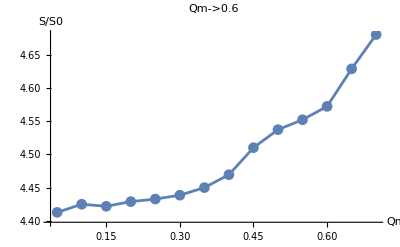

```mathematica
ListLinePlot[Table[{0.05m,shrink[{Qm->0.6,μ->3000}][[m]]},{m,1,14}],AxesLabel->{"Qm","S/S0"},PlotRange->All,PlotMarkers->Automatic,PlotLabel->"Qm->0.6"]
```

```mathematica
σk=Association[];
σk[{a->0.3,μ->3000}]=Table[√(1/(2π)NIntegrate[((1/shapedata[{a->0.3,μ->0}][[m,8]][α])(shapedata[{a->0.3,μ->3000}][[m,8]][α]-shapedata[{a->0.3,μ->00}][[m,8]][α]))^2,{α,0,2π}]),{m,1,16}];
σk[{Qm->0.6,μ->3000}]=Table[√(1/(2π)NIntegrate[((1/shapedata[{Qm->0.6,μ->0}][[m,8]][α])(shapedata[{Qm->0.6,μ->3000}][[m,8]][α]-shapedata[{Qm->0.6,μ->00}][[m,8]][α]))^2,{α,0,2π}]),{m,1,14}];
σk
```

<|{a→0.3,μ→3000}→{0.0328413,0.114707,0.218729,0.325235,0.428766,0.527854,0.625411,0.725316,0.818145,0.914251,1.00975,1.10711,1.21061,1.31641,1.43117,1.56196},{Qm→0.6,μ→3000}→{1.10106,1.1038,1.10304,1.1047,1.10594,1.10711,1.10986,1.11449,1.1243,1.131,1.13445,1.13984,1.15383,1.16669}|>

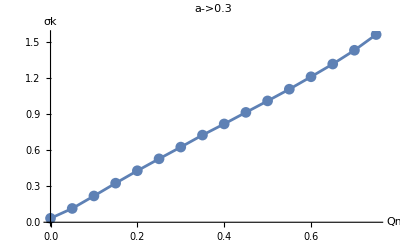

```mathematica
ListLinePlot[Table[{0.05m-0.05,σk[{a->0.3,μ->3000}][[m]]},{m,1,16}],AxesLabel->{"Qm","σk"},PlotRange->All,PlotMarkers->Automatic,PlotLabel->"a->0.3"]
```

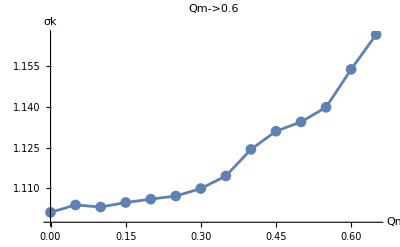

```mathematica
ListLinePlot[Table[{0.05m-0.05,σk[{Qm->0.6,μ->3000}][[m]]},{m,1,14}],AxesLabel->{"Qm","σk"},PlotRange->All,PlotMarkers->Automatic,PlotLabel->"Qm->0.6"]
```